## Matrix Element calculation (including time evolution)

```mathematica
Clear[ω,ωt,t]
```

```mathematica
L =3.*10^-7; Lstep =1.*10^-8; LN = 2.*L/Lstep + 1.;nmax = 15.;c = 2.997 10^8;hbar = 1.0545718×10^-34;m = 132.90 * 1.660539 10^-27 ; 
Uprop[x_,xt_,t_,ωt_]:= ((m ωt)/(2 Pi ⅈ hbar Sin[ ωt  t]))^(1/2)Exp[(ⅈ m ωt)/(2 hbar Sin[ωt t])((x^2+xt^2) Cos[ωt t ] - 2 x xt)]
deltak = 2 Pi/(455 10^-9)//N
ψ[x_, n_, ω_]:= 1/Sqrt[2^n n!]((m ω)/(Pi hbar))^(1/4)Exp[(-m ω x^2)/(2 hbar)]HermiteH[n, Sqrt[(m ω)/hbar]x]Exp[ⅈ  deltak x]
ψf[xt_, nt_, ωt_]:= 1/Sqrt[2^nt nt!]((m ωt)/(Pi hbar))^(1/4)Exp[(-m ωt xt^2)/(2 hbar)]HermiteH[nt, Sqrt[(m ωt)/hbar]xt]
```

1.38092×10^7

```mathematica
omega[3]
omega[4]
```

```mathematica
2*52564.18722654877
```

105128.

```mathematica
2 Pi/(30 10^-6)//N
```

209440.

```mathematica
2*96487.56959133178
```

192975.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

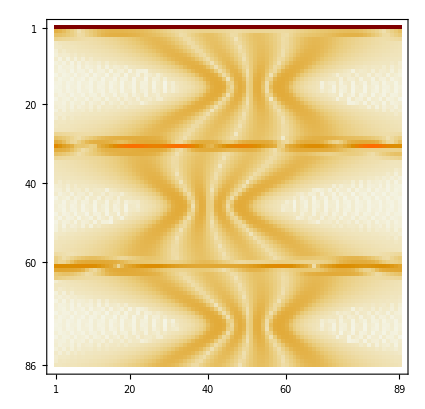

```mathematica
L =0.4*10^-6; Lstep =0.09*10^-7; LN = 2*L/Lstep + 1;
psi[t_, xt_,ω_,ωt_, n_] :=  Lstep*Sum[ψ[x, n, ω]*  Uprop[x,xt,t,ωt],{x,-L,L,Lstep}]
Monitor[evolmat = Table[Abs[psi[t, xt,omega[3],omega[5], 3]]^2,{t,0,60000 10^-9, 700 10^-9},{xt, -L, L, Lstep}];,{(t/(400 10^-9))//N,(xt/L)}]
MatrixPlot[evolmat]
```

```mathematica
nmax = 15.;c = 2.997 10^8;hbar = 1.0545718×10^-34;m = 132.90 * 1.660539 10^-27 ; 
L =0.8*10^-6; Lstep =0.2*10^-7; LN = 2*L/Lstep + 1;
deltak = 2 Pi/(455 10^-9)//N;
```

```mathematica
UPn[ω_, ωt_,n_, nt_, t_] := Lstep^2 *Sum[ 1/Sqrt[2^nt nt!]((m ωt)/(Pi hbar))^(1/4)Exp[(-m ωt xt^2)/(2 hbar)]HermiteH[nt, Sqrt[(m ωt)/hbar]xt]*1/Sqrt[2^n n!]((m ω)/(Pi hbar))^(1/4)Exp[(-m ω x^2)/(2 hbar)]HermiteH[n, Sqrt[(m ω)/hbar]x]Exp[ⅈ  deltak x]* ((m ωt)/(2 Pi ⅈ hbar Sin[ ωt  t]))^(1/2)Exp[(ⅈ m ωt)/(2 hbar Sin[ωt t])((x^2+xt^2) Cos[ωt t ] - 2 x xt)],{x,-L,L,Lstep}, {xt,-L,L,Lstep}]
```

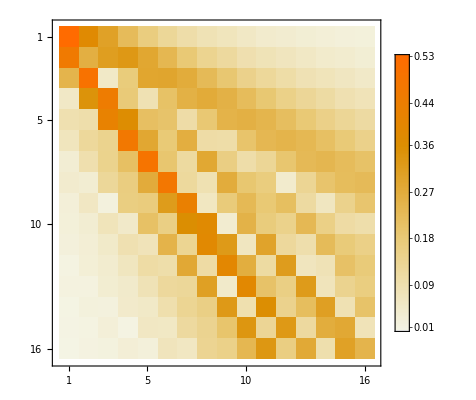

```mathematica
Monitor[ω = omega[1]; ωt=omega[2]; t= 10^-5;uma = Table[Abs[Lstep^2 *Sum[1/Sqrt[2^nt nt!]((m ωt)/(Pi hbar))^(1/4)Exp[(-m ωt xt^2)/(2 hbar)]HermiteH[nt, Sqrt[(m ωt)/hbar]xt]*1/Sqrt[2^n n!]((m ω)/(Pi hbar))^(1/4)Exp[(-m ω x^2)/(2 hbar)]HermiteH[n, Sqrt[(m ω)/hbar]x]*Exp[ⅈ  deltak x]* ((m ωt)/(2 Pi ⅈ hbar Sin[ ωt  t]))^(1/2)Exp[(ⅈ m ωt)/(2 hbar Sin[ωt t])((x^2+xt^2) Cos[ωt t ] - 2 x xt)],{x,-L,L,Lstep}, {xt,-L,L,Lstep}]]^2,{n,0.,nmax},{nt,0.,nmax}];,{n,nt}]
MatrixPlot[uma, PlotLegends -> True]
```

## Calculate matrix elements for all segments (Are the decay times of the order of typical ωt? Here: assumed much smaller)

```mathematica
(*from LambDickeParams_Singe.py @532nm and @10**7 lattice beam intensity *)
(*levels=["6s 2 S 1/2","7p 2 P ?3/2","7s 2 S 1/2","6p 2 P ?1/2","6p 2 P ?3/2","5d 2 D 3/2","5d 2 D 5/2"]*)
(*decays=[l21,l23,l35,l41,l64,l51,l65,l75,l27,l26,l34]*)
omegas = {93404.36151476773,58312.21388517295,52564.18722654877,96487.56959133178,149378.74074871602,114323.656390064,134446.8575802304};
etas = {0.697646827167697,0.14448683087878345,0.17095247621856766,0.35533728030290285,0.10383570605450117,0.3729352538139725,0.06952852571696208,0.07198024772090308,0.19467123685222815,0.21390857630773225,0.23003214721947357};
l21=455.5*10^-9;
l23=2931.8*10^-9;
l35=1469.9*10^-9;
l41=894.3*10^-9;
l64=3011.1*10^-9;
l51=852.1*10^-9;
l65=3614.1*10^-9;
l75=3491*10^-9;
l27=1360.6*10^-9;
l26=1342.8*10^-9;
l34=1359.2*10^-9;
decays={l21,l23,l35,l41,l64,l51,l65,l75,l27,l26,l34};
g23=4.05*10^6;
g34=6.23*10^6;
g35=11.4*10^6;
g41=28.6*10^6;
g26=0.13*10^6;
g27=1.10*10^6;
g75=0.78*10^6;
g65=0.11*10^6;
g51=32.8*10^6;
g64=0.91*10^6;
g21=1.84*10^6;
gammas={g21,g23,g35,g41,g64,g51,g65,g75,g27,g26,g34};
omega[n_]:= omegas[[n]]
eta[n_]:= etas[[n]]
nmax = 15.;c = 2.997 10^8;hbar = 1.0545718×10^-34;m = 132.90 * 1.660539 10^-27 ; 
L =0.4*10^-6; Lstep =0.09*10^-7; LN = 2*L/Lstep + 1;deltak = 2 Pi/(455 10^-9)//N;
```

```mathematica
Clear[t]
```

```mathematica
(*IntU[ω_,ωt_,τ_]:= Monitor[tstart = τ/10;tstop = 3*τ //N; tstep =(tstop/5)//N;*)
IntU[ω_,ωt_,τ_]:= Monitor[tstart =1.5 10^6;tstop = 1.5 10^-6 //N; tstep =τ//N; t = tstart;uma = Table[
Abs[Lstep^2 *Sum[1/Sqrt[2^nt nt!]((m ωt)/(Pi hbar))^(1/4)Exp[(-m ωt xt^2)/(2 hbar)]HermiteH[nt, Sqrt[(m ωt)/hbar]xt]*1/Sqrt[2^n n!]((m ω)/(Pi hbar))^(1/4)Exp[(-m ω x^2)/(2 hbar)]HermiteH[n, Sqrt[(m ω)/hbar]x]*Exp[ⅈ  deltak x]* ((m ωt)/(2 Pi ⅈ hbar Sin[ ωt  t]))^(1/2)Exp[(ⅈ m ωt)/(2 hbar Sin[ωt t])((x^2+xt^2) Cos[ωt t ] - 2 x xt)],{x,-L,L,Lstep}, {xt,-L,L,Lstep}]]^2,{n,0.,nmax},{nt,0.,nmax}] ,{n,nt,t//N}];(*Abs[Lstep^2 *Sum[1/Sqrt[2^nt nt!]((m ωt)/(Pi hbar))^(1/4)Exp[(-m ωt xt^2)/(2 hbar)]HermiteH[nt, Sqrt[(m ωt)/hbar]xt]*1/Sqrt[2^n n!]((m ω)/(Pi hbar))^(1/4)Exp[(-m ω x^2)/(2 hbar)]HermiteH[n, Sqrt[(m ω)/hbar]x]*Exp[ⅈ  deltak x]* ((m ωt)/(2 Pi ⅈ hbar Sin[ ωt  t]))^(1/2)Exp[(ⅈ m ωt)/(2 hbar Sin[ωt t])((x^2+xt^2) Cos[ωt t ] - 2 x xt)],{x,-L,L,Lstep}, {xt,-L,L,Lstep}]]^2,{n,0.,nmax},{nt,0.,nmax}] Exp[-t/τ]/τ,{t,tstart, tstop, tstep}],{n,nt,t//N}]*)
Drw[n_,nt_, η_, θ_]:= √((Min[n,nt]!)/((Min[n,nt]+Abs[nt-n])!))(ⅈ η  Cos[θ])^Abs[nt-n] LaguerreL[Min[n,nt],Abs[nt-n],(η  Cos[θ])^2]Exp[-(η  Cos[θ])^2/2];
IntDr[η_]:= Table[1/(2 Pi /(Pi/100.5))Sum[Abs[√((Min[n,nt]!)/((Min[n,nt]+Abs[nt-n])!))(ⅈ η  Cos[θ])^Abs[nt-n] LaguerreL[Min[n,nt],Abs[nt-n],(η  Cos[θ])^2]Exp[-(η  Cos[θ])^2/2]]^2,{θ,0, 2 Pi, Pi/100.5}],{n,0.,nmax},{nt,0.,nmax}];
IntD[η_]:= Table[Abs[√((Min[n,nt]!)/((Min[n,nt]+Abs[nt-n])!))(ⅈ η  1)^Abs[nt-n] LaguerreL[Min[n,nt],Abs[nt-n],(η  1)^2]Exp[-(η  1)^2/2]]^2,{n,0.,nmax},{nt,0.,nmax}];
```

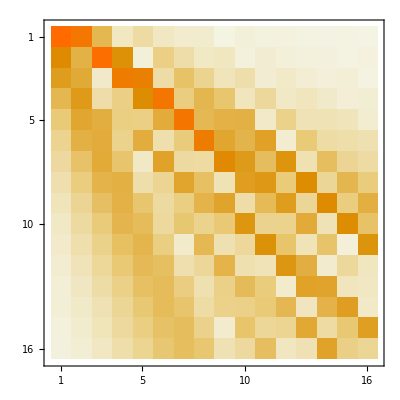

```mathematica
MatrixPlot[IntU[omega[3],omega[4], 1/g34 //N]] (*test*)
```

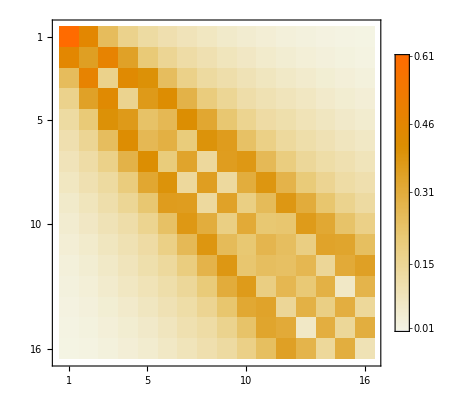

```mathematica
MatrixPlot[IntD[0.7], PlotLegends -> True] (*test*)
```

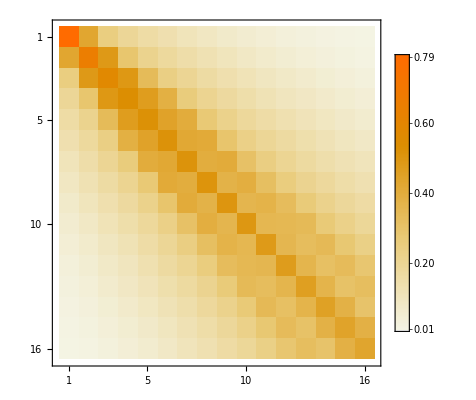

```mathematica
MatrixPlot[IntDr[0.7], PlotLegends -> True] (*test*)
```

Power::indet: Indeterminate expression (0.+0. ⅈ)^0 encountered.

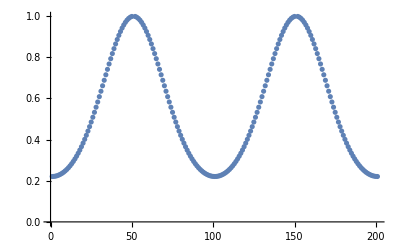

```mathematica
ListPlot[Table[Abs[Drw[15,15, 0.2, θ]]^2,{θ,0, 2 Pi, Pi/100}]]
```

```mathematica
U12= IntU[omega[1],omega[2], (1/g21) //N];
U23 = IntU[omega[2],omega[3], (1/g23) //N];
U35 = IntU[omega[3],omega[5], (1/g35) //N];
U41 = IntU[omega[4],omega[1], (1/g41) //N];
U64 = IntU[omega[6],omega[4], (1/g64) //N];
U51 = IntU[omega[5],omega[1], (1/g51) //N];
U65 = IntU[omega[6],omega[5], (1/g65) //N];
U75 = IntU[omega[7],omega[5], (1/g75) //N];
U27 = IntU[omega[2],omega[7], (1/g27) //N];
U26 = IntU[omega[2],omega[6], (1/g26) //N];
U34 = IntU[omega[3],omega[4], (1/g34) //N];
```

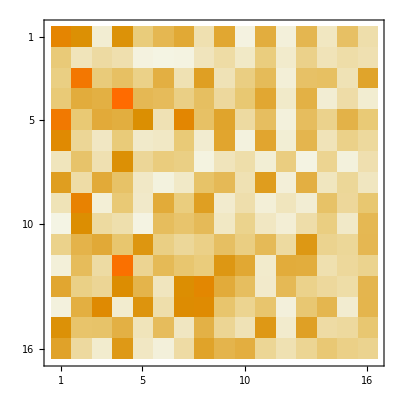

```mathematica
MatrixPlot[U35]
```

```mathematica
D12 = IntD[eta[1]];
D21 = IntDr[eta[1]];
D23 = IntDr [eta[2]];
D35 = IntDr[eta[3]];
D41 = IntDr[eta[4]];
D64 = IntDr[eta[5]];
D51 = IntDr[eta[6]];
D65 = IntDr[eta[7]];
D75 = IntDr[eta[8]];
D27 = IntDr[eta[9]];
{{D26 = IntDr[eta[10]];}, {D34 = IntDr[eta[11]];}}
```

{{Null},{Null}}

```mathematica
pathA = D41.U34.D34.U23.D23.U12.D12; (*7p3/2 -> 7s1/2 -> 6p1/2-> 6s1/2*)
pathB = D51.U35.D35.U23.D23.U12.D12;(*7p3/2 -> 7s1/2 -> 6p3/2-> 6s1/2*)
pathC = D51.U65.D65.U26.D26.U12.D12;(*7p3/2 -> 5d3/2 -> 6p3/2-> 6s1/2*)
pathD = D41.U64.D64.U26.D26.U12.D12;(*7p3/2 -> 5d3/2 -> 6p1/2-> 6s1/2*)
pathE = D51.U75.D75.U27.D27.U12.D12;(*7p3/2 -> 5d3/2 -> 6p1/2-> 6s1/2*)
pathF = D21.U12.D12;(*7p3/2 -> 5d3/2 -> 6p1/2-> 6s1/2*)
```

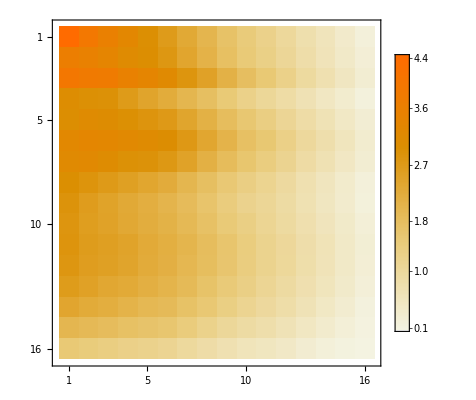

```mathematica
MatrixPlot[pathE, PlotLegends -> True]
```

```mathematica
pathTot = 0.201004*pathA +0.3678 pathB +0.001969 pathC + 0.016289pathD + 0.154494pathE + 0.258427 pathF
```

{{8.57749,7.67632,6.87327,6.39759,5.937,5.35846,5.3034,4.41046,4.96168,4.20078,3.98475,3.92923,2.94168,2.35603,2.24748,1.90327},{7.52769,6.59242,5.97795,5.29182,4.75183,4.24626,4.09261,3.38329,3.67651,3.12308,2.95855,2.88223,2.16955,1.7279,1.65481,1.36634},{4.15511,3.91072,3.86547,3.74423,3.6196,3.45243,3.57009,2.99042,3.46407,2.88322,2.76469,2.77641,2.08524,1.64859,1.58778,1.33085},{5.70324,5.18227,4.50846,4.3481,4.11123,3.72668,3.71358,3.07767,3.52464,2.96627,2.83685,2.82468,2.10577,1.68177,1.60324,1.35912},{5.56301,5.15367,4.7321,4.52205,4.30711,3.96951,3.98613,3.31513,3.78569,3.19279,3.06067,3.03853,2.28151,1.81566,1.74275,1.45761},{6.32409,5.79445,5.41387,5.01667,4.72827,4.37518,4.37969,3.63698,4.09624,3.46538,3.29316,3.25525,2.44623,1.95915,1.87969,1.58198},{7.43054,6.63561,6.06196,5.4282,4.99009,4.53359,4.42428,3.6563,4.00291,3.41632,3.22165,3.14163,2.37432,1.89469,1.82277,1.51484},{7.32209,6.47762,5.85826,5.26734,4.80937,4.32892,4.20105,3.47787,3.81181,3.24344,3.0782,2.99971,2.26581,1.79414,1.73119,1.42029},{6.15523,5.57605,5.05287,4.6876,4.39144,4.00839,3.95662,3.28005,3.67198,3.11298,2.97614,2.92818,2.20863,1.75163,1.68942,1.39302},{4.99628,4.73671,4.43453,4.26124,4.13704,3.89158,3.94463,3.28928,3.73998,3.16643,3.02552,3.00378,2.27148,1.8083,1.74528,1.45325},{4.55742,4.44597,4.27288,4.16179,4.13527,3.96389,4.07859,3.40663,3.90467,3.30783,3.15421,3.14075,2.37914,1.90279,1.8359,1.54068},{4.61338,4.55013,4.39517,4.28697,4.31531,4.15967,4.29688,3.57754,4.12489,3.49571,3.34086,3.32724,2.52151,2.02387,1.95065,1.64059},{4.65249,4.67573,4.52937,4.4503,4.5226,4.37161,4.51719,3.75136,4.34757,3.68511,3.53914,3.52843,2.67456,2.1494,2.06823,1.73622},{4.40549,4.53644,4.42741,4.39926,4.50237,4.36693,4.51753,3.74249,4.36281,3.69275,3.56512,3.56444,2.70039,2.16731,2.08338,1.74532},{3.68571,3.86,3.7905,3.79986,3.90343,3.79598,3.93281,3.25461,3.81043,3.22099,3.11912,3.12686,2.36673,1.89698,1.82203,1.52739},{2.69093,2.81749,2.78231,2.79085,2.86734,2.79486,2.90269,2.40084,2.81887,2.38131,2.30784,2.31758,1.75287,1.40364,1.34731,1.13104}}